This is the original network:

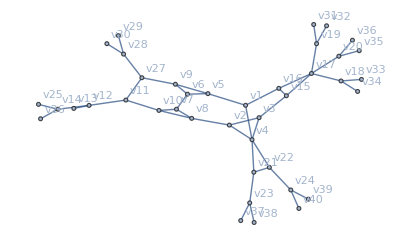

number of vertices in network: 40

number of edges in network: 47

edge list of network: {v1<->v5,v1<->v4,v1<->v16,v2<->v3,v2<->v4,v2<->v8,v3<->v4,v3<->v15,v4<->v21,v4<->v22,v5<->v6,v5<->v9,v6<->v7,v6<->v9,v7<->v8,v7<->v10,v8<->v10,v10<->v11,v11<->v12,v12<->v13,v12<->v14,v15<->v16,v15<->v17,v16<->v17,v17<->v18,v17<->v19,v17<->v20,v21<->v22,v21<->v23,v22<->v24,v14<->v25,v14<->v26,v11<->v27,v27<->v9,v27<->v28,v28<->v29,v28<->v30,v19<->v31,v19<->v32,v18<->v33,v18<->v34,v20<->v35,v20<->v36,v23<->v37,v23<->v38,v24<->v39,v24<->v40}

This is the core of your network:

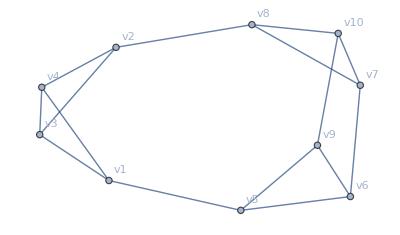

number of vertices in core: 10

number of edges in core: 15

edge list of core: {v1<->v5,v1<->v4,v2<->v3,v2<->v4,v2<->v8,v3<->v4,v5<->v6,v5<->v9,v6<->v7,v6<->v9,v7<->v8,v7<->v10,v8<->v10,v1<->v3,v9<->v10}

This is the kernel of your network:

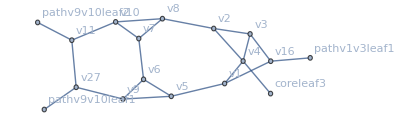

number of vertices in kernel: 17

number of edges in kernel: 22

edge list of kernel: {v1<->v5,v1<->v4,v2<->v4,v2<->v3,v3<->v4,v2<->v8,v5<->v6,v5<->v9,v6<->v9,v6<->v7,v7<->v8,v7<->v10,v8<->v10,v1<->v16,v27<->v9,v10<->v11,v11<->v27,coreleaf3<->v4,pathv1v3leaf1<->v16,pathv9v10leaf1<->v27,pathv9v10leaf2<->v11,v3<->v16}

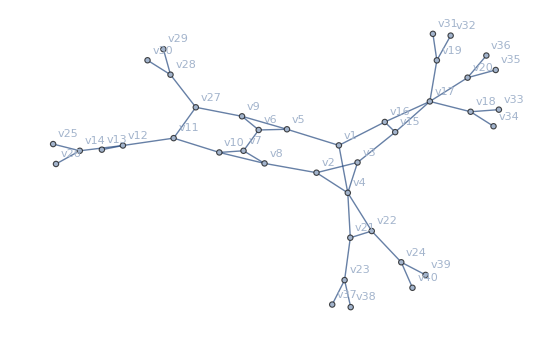

number of vertices in network: 40

number of edges in network: 47

edge list of network: {v1<->v5,v1<->v4,v1<->v16,v2<->v3,v2<->v4,v2<->v8,v3<->v4,v3<->v15,v4<->v21,v4<->v22,v5<->v6,v5<->v9,v6<->v7,v6<->v9,v7<->v8,v7<->v10,v8<->v10,v10<->v11,v11<->v12,v12<->v13,v12<->v14,v15<->v16,v15<->v17,v16<->v17,v17<->v18,v17<->v19,v17<->v20,v21<->v22,v21<->v23,v22<->v24,v14<->v25,v14<->v26,v11<->v27,v27<->v9,v27<->v28,v28<->v29,v28<->v30,v19<->v31,v19<->v32,v18<->v33,v18<->v34,v20<->v35,v20<->v36,v23<->v37,v23<->v38,v24<->v39,v24<->v40}

This is the core of your network:

-Graphics-

number of vertices in core: 10

number of edges in core: 15

edge list of core: {v1<->v5,v1<->v4,v2<->v3,v2<->v4,v2<->v8,v3<->v4,v5<->v6,v5<->v9,v6<->v7,v6<->v9,v7<->v8,v7<->v10,v8<->v10,v1<->v3,v9<->v10}

This is the kernel of your network:

-Graphics-

number of vertices in kernel: 17

number of edges in kernel: 22

edge list of kernel: {v1<->v5,v1<->v4,v2<->v4,v2<->v3,v3<->v4,v2<->v8,v5<->v6,v5<->v9,v6<->v9,v6<->v7,v7<->v8,v7<->v10,v8<->v10,v1<->v16,v27<->v9,v10<->v11,v11<->v27,coreleaf3<->v4,pathv1v3leaf1<->v16,pathv9v10leaf1<->v27,pathv9v10leaf2<->v11,v3<->v16}

```mathematica
If[ChoiceDialog["Do you wish to use an input file or do you want to enter the edge set of your phylogenetic network manually?",{"Load input file"->"a","Enter edge set manually"->"b"}]=="b",edgeset=Input["Please enter the edge set of your phylogenetic network and then press ENTER on your keyboard."],edgeset=ToExpression[Import[Input["Please enter the file name including the path and then press ENTER on your keyboard."]]]];

network=Graph[edgeset,VertexLabels->"Name"];

core=getCore[network];
kernel=getKernel[network];

Print["This is the original network: "];
Print[network];
Print["number of vertices in network: ",VertexCount[network]];
Print["number of edges in network: ",EdgeCount[network]];
Print["edge list of network: ",edgeset];
Print[];
Print[];
Print["This is the core of your network: "];
Print[core];
Print["number of vertices in core: ",VertexCount[core]];
Print["number of edges in core: ",EdgeCount[core]];
Print["edge list of core: ",EdgeList[core]];
Print[];
Print[];
Print["This is the kernel of your network: "];
Print[kernel];
Print["number of vertices in kernel: ",VertexCount[kernel]];
Print["number of edges in kernel: ",EdgeCount[kernel]];
Print["edge list of kernel: ",EdgeList[kernel]];
Print[];
Print[];
If[ChoiceDialog["Shall an attempt be made to test your network for treebasedness?",{"Yes"->True,"No"->False}],time=Input["How many seconds (CPU time) shall be spent on the attempt? Enter a number or the word Infinity and press ENTER on your keyboard."];Print[];Print[];
TimeConstrained[If[ExtendedTreeBasedQ[kernel],choice=ChoiceDialog["Great, your network is treebased and a support tree of the kernel of your network has already been printed! Do you now want to see ALL support trees of the kernel?",{"I need all"->"b","No thanks"->"c"}];

If[choice=="b",timenew=Input["How many seconds (CPU time) shall be spent on the attempt? Enter a number or the word Infinity and press ENTER on your keyboard." ];Print["All support trees of the network kernel: "];TimeConstrained[Print[getAllSupportTrees[kernel][[1]]],timenew,Print[Style["The specified time was unfortunately not sufficient to find all spanning trees of the kernel.",FontColor->"Red"]]]],Print[Style["Your network is NOT treebased!",FontColor->Red]]],time,Print[Style["The specified time was unfortunately not sufficient to examine treebasedness.",FontColor->"Red"]]];





];
```

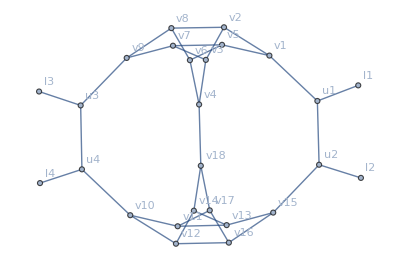

```mathematica
g=Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"},VertexLabels->"Name"]
```

```mathematica
FindASupportTree[Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"}]]
```

$Aborted

```mathematica
list=getAllSpanningTrees[Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"}]];
```

$Aborted

```mathematica
getGeneralizedKirchhoffMatrix[g]//Length
```

26

```mathematica
getKirchhoffPolynomial[g]
```

$Aborted

```mathematica
Length[list]
```

```mathematica
numberOfSpanningTrees[Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"}]]
```

2246400

```mathematica
TreeBasedQ[getKernel[Graph[{"v1"<->"v5","v1"<->"v4","v1"<->"v16","v2"<->"v3","v2"<->"v4","v2"<->"v8","v3"<->"v4","v3"<->"v15","v4"<->"v21","v4"<->"v22","v5"<->"v6","v5"<->"v9","v6"<->"v7","v6"<->"v9","v7"<->"v8","v7"<->"v10","v8"<->"v10","v10"<->"v11","v11"<->"v12","v12"<->"v13","v12"<->"v14","v15"<->"v16","v15"<->"v17","v16"<->"v17","v17"<->"v18","v17"<->"v19","v17"<->"v20","v21"<->"v22","v21"<->"v23","v22"<->"v24","v14"<->"v25","v14"<->"v26","v11"<->"v27","v27"<->"v9","v27"<->"v28","v28"<->"v29","v28"<->"v30","v19"<->"v31","v19"<->"v32","v18"<->"v33","v18"<->"v34","v20"<->"v35","v20"<->"v36","v23"<->"v37","v23"<->"v38","v24"<->"v39","v24"<->"v40"}]]]
```

True

Your network is treebased!

This is a support tree:

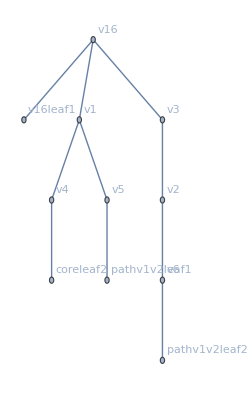

edge set of the support tree: {v16<->v16leaf1,v1<->v16,v1<->v4,v1<->v5,v2<->v3,v2<->v6,v3<->v16,v4<->coreleaf2,v5<->pathv1v2leaf1,v6<->pathv1v2leaf2}

True

```mathematica
ExtendedTreeBasedQ[getKernel[Graph[{"v1"<->"v5","v1"<->"v4","v1"<->"v16","v2"<->"v3","v2"<->"v4","v2"<->"v8","v3"<->"v4","v3"<->"v15","v4"<->"v21","v4"<->"v22","v5"<->"v6","v5"<->"v9","v6"<->"v7","v6"<->"v9","v7"<->"v8","v7"<->"v10","v8"<->"v10","v10"<->"v11","v11"<->"v12","v12"<->"v13","v12"<->"v14","v15"<->"v16","v15"<->"v17","v16"<->"v17","v17"<->"v18","v17"<->"v19","v17"<->"v20","v21"<->"v22","v21"<->"v23","v22"<->"v24","v14"<->"v25","v14"<->"v26","v11"<->"v27","v27"<->"v9","v27"<->"v28","v28"<->"v29","v28"<->"v30","v19"<->"v31","v19"<->"v32","v18"<->"v33","v18"<->"v34","v20"<->"v35","v20"<->"v36","v23"<->"v37","v23"<->"v38","v24"<->"v39","v24"<->"v40"}]]]
```

```mathematica
g=Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"},VertexLabels->"Name"]
```

-Graphics-

```mathematica
getAllSupportTrees[g]
```

$Aborted

```mathematica
FindASupportTree[g]
```

$Aborted

```mathematica
edge=Input[]
```

```mathematica
edge
```

```mathematica
Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"},VertexLabels->"Name"]
```

-Graphics-

```mathematica
g=Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"},VertexLabels->"Name"]
```

-Graphics-

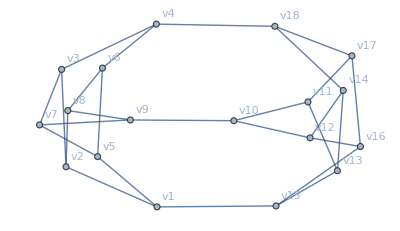

```mathematica
LeafShrinking[g]
```

```mathematica
EdgebasedQ[g]
```

False

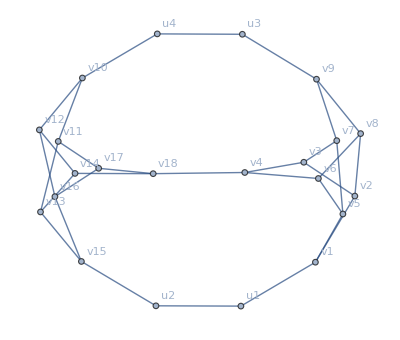

```mathematica
LeafCutting[g]
```

```mathematica
getCore[g]
```

-Graphics-

```mathematica
getKernel[g]
```

```mathematica
Levelk[g]
```

ConnectedComponents::graph: A graph object is expected at position 1 in ConnectedComponents[EdgeDelete[g,g]].

VertexList::graph: A graph object is expected at position 1 in VertexList[EdgeDelete[g,g]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[EdgeDelete[g,g]].

EdgeDelete::graph: A graph object is expected at position 1 in EdgeDelete[EdgeDelete[g,g],EdgeDelete[g,g]].

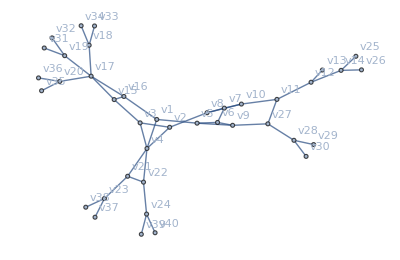

```mathematica
example=Graph[{"v1","v2","v3","v4","v5","v6","v7","v8","v9","v10","v11","v12","v13","v14","v15","v16","v17","v18","v19","v20","v21","v22","v23","v24"},{"v1"<->"v5","v1"<->"v4","v1"<->"v16","v2"<->"v3","v2"<->"v4","v2"<->"v8","v3"<->"v4","v3"<->"v15","v4"<->"v21","v4"<->"v22","v5"<->"v6","v5"<->"v9","v6"<->"v7","v6"<->"v9","v7"<->"v8","v7"<->"v10","v8"<->"v10","v10"<->"v11","v11"<->"v12","v12"<->"v13","v12"<->"v14","v15"<->"v16","v15"<->"v17","v16"<->"v17","v17"<->"v18","v17"<->"v19","v17"<->"v20","v21"<->"v22","v21"<->"v23","v22"<->"v24","v14"<->"v25","v14"<->"v26","v11"<->"v27","v27"<->"v9","v27"<->"v28","v28"<->"v29","v28"<->"v30","v19"<->"v31","v19"<->"v32","v18"<->"v33","v18"<->"v34","v20"<->"v35","v20"<->"v36","v23"<->"v37","v23"<->"v38","v24"<->"v39","v24"<->"v40"},VertexLabels->"Name"]
```

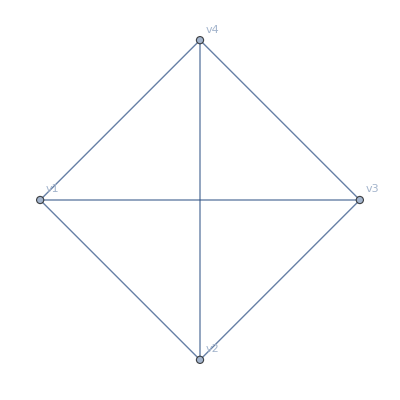

```mathematica
getCore[example]
```

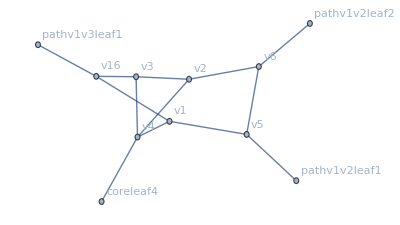

```mathematica
getKernel[example]
```

```mathematica
TreebasedQ[getKernel[example]]
```

True

```mathematica
getCore[g]
```

-Graphics-

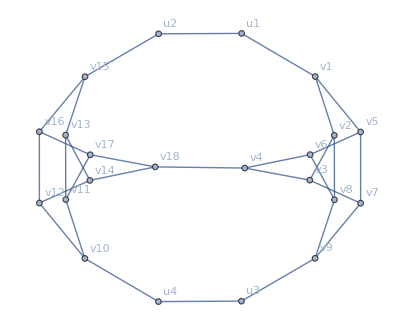
{-Graphics-,{{v1<->v15,{v1,u1,u2,v15}},{v9<->v10,{v9,u3,u4,v10}}},-Graphics-}

```mathematica
getExtendedCore[g]
```

```mathematica
NumberOfExitPaths[g,{"v1","u1","u2","v15"}]
```

2

```mathematica
NumberOfExitPaths[g,{"v9","u3","u4","v10"}]
```

2

```mathematica
getKernel[g]
```

```mathematica
TreePruning[g]
```

-Graphics-

```mathematica
IsTreeQ[g]
```

False

```mathematica
g=Graph[{"v1"<->"v2","v1"<->"v5","v1"<->"u1","v2"<->"v3","v2"<->"v8","v3"<->"v4","v3"<->"v7","v4"<->"v6","v4"<->"v18","v5"<->"v6","v5"<->"v7","v6"<->"v8","v7"<->"v9","v8"<->"v9","v9"<->"u3","u1"<->"l1","u1"<->"u2","u2"<->"l2","u2"<->"v15","u3"<->"l3","u3"<->"u4","u4"<->"l4","u4"<->"v10","v10"<->"v11","v10"<->"v12","v11"<->"v13","v11"<->"v17","v12"<->"v14","v12"<->"v16","v13"<->"v14","v13"<->"v15","v14"<->"v18","v15"<->"v16","v16"<->"v17","v17"<->"v18"},VertexLabels->"Name"]
```

-Graphics-

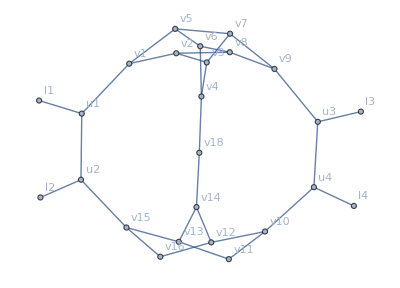

```mathematica
VertexDelete[g,"v17"]
```

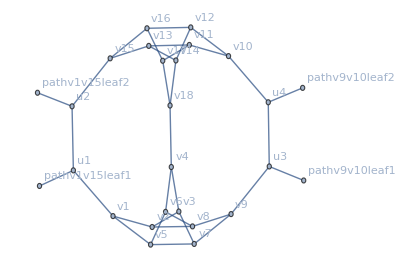

```mathematica
getKernel[g]
```

```mathematica
TreeBasedQ[g]
```

True

```mathematica
getGeneralizedKirchhoffMatrix[simplegraph_]:=Module[{edgeset,vertexset,matrix,node1,node2,i,j,rowsums},
edgeset=EdgeList[simplegraph];
vertexset=VertexList[simplegraph];
matrix=Table[0,{i,1,Length[vertexset]},{j,1,Length[vertexset]}];

For[i=1,i≤Length[vertexset]-1,i++,
For[j=i+1,j≤Length[vertexset],j++,

node1=vertexset[[i]];
node2=vertexset[[j]];

If[MemberQ[AdjacencyList[simplegraph,node1],node2],matrix[[i]][[j]]=StringJoin["e_",ToString[node1],"-",ToString[node2]];matrix[[j]][[i]]=matrix[[i]][[j]]];


];];

rowsums=Table[0,{i,1,Length[vertexset]}];
For[i=1,i≤Length[vertexset],i++,
For[j=1,j≤Length[vertexset],j++,
rowsums[[i]]=rowsums[[i]]+matrix[[i]][[j]];


]

];

For[i=1,i≤Length[vertexset],i++,
matrix[[i]][[i]]=-rowsums[[i]];
];

Return[matrix];








]
getKirchhoffPolynomial[simplegraph_]:=Module[{mat,n,matnew},mat=getGeneralizedKirchhoffMatrix[simplegraph];
n=Length[mat];
matnew=Delete[mat,Length[mat]];
matnew=Transpose[matnew];
matnew=Delete[matnew,Length[matnew]];
matnew=Transpose[matnew];
Return[ExpandAll[Det[matnew]]];


];
getAllSpanningTrees[simplegraph_]:=Module[{treelist,spanningtrees,i},
treelist=StringSplit[ToString[getKirchhoffPolynomial[getKernel[example]]],"+"];
For[i=1,i≤Length[treelist],i++,
treelist[[i]]=StringDelete[treelist[[i]],"e_"];
treelist[[i]]=StringReplace[treelist[[i]]," "->","];
If[i>1,treelist[[i]]=StringDrop[treelist[[i]],1]];
If[i<Length[treelist],treelist[[i]]=StringDrop[treelist[[i]],-1]];
treelist[[i]]=StringReplace[treelist[[i]],"-"->"<->"];

treelist[[i]]=ToExpression[StringSplit[treelist[[i]],","]];

];

spanningtrees={};
For[i=1,i≤Length[treelist],i++,
AppendTo[spanningtrees,Graph[treelist[[i]],VertexLabels->"Name"]];


];

Return[spanningtrees];




];
getAllSupportTrees[phylonetwork_]:=Module[{spanningtrees,i,supporttrees,leafnumber},spanningtrees=getAllSpanningTrees[phylonetwork];
supporttrees={};
leafnumber=Count[VertexDegree[phylonetwork],1];

For[i=1,i≤Length[spanningtrees],i++,
If[Count[VertexDegree[spanningtrees[[i]]],1]==leafnumber,AppendTo[supporttrees,spanningtrees[[i]]]];



];
Return[{supporttrees,Length[supporttrees]}];


];
FindASupportTree[phylonetwork_]:=Module[{spanningtrees,i,supporttrees,leafnumber},spanningtrees=getAllSpanningTrees[phylonetwork];
supporttrees={};
leafnumber=Count[VertexDegree[phylonetwork],1];

For[i=1,i≤Length[spanningtrees],i++,
If[Count[VertexDegree[spanningtrees[[i]]],1]==leafnumber,AppendTo[supporttrees,spanningtrees[[i]]];Break[]];



];
Return[supporttrees];


];
TreeBasedQ[phylonetwork_]:=Module[{},If[FindASupportTree[phylonetwork]≠{},Return[True],Return[False]]];
```

```mathematica
TreeBasedQ[getKernel[example]]
```

True

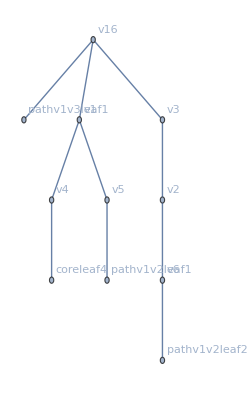
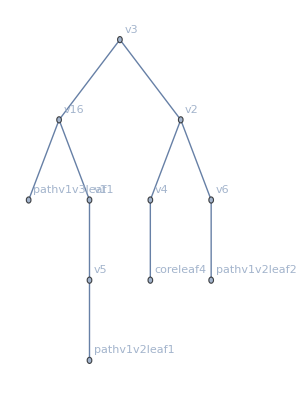
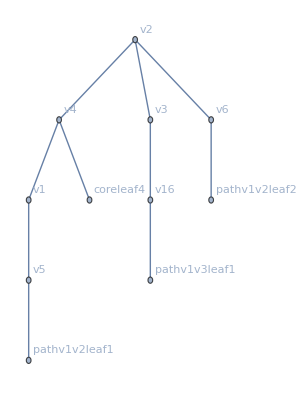
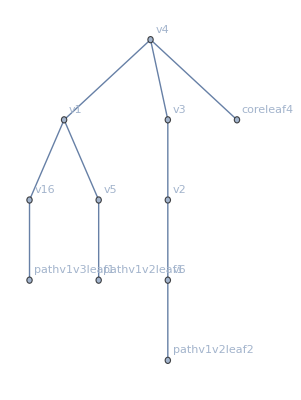
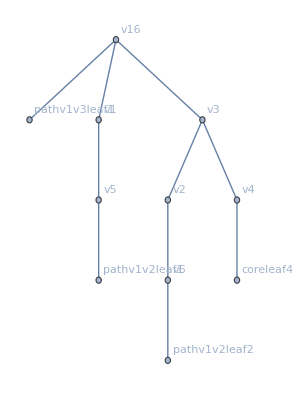
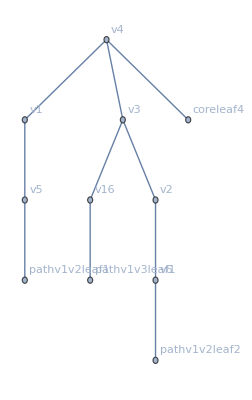
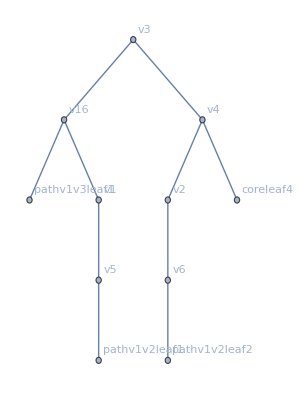
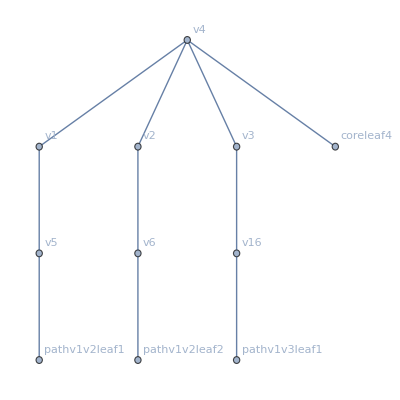

```mathematica
getAllSupportTrees[getKernel[example]]
```

```mathematica
getKernel[example]
```

-Graphics-

```mathematica
tree=getAllSpanningTrees[getKernel[example]][[5]]
```

-Graphics-

```mathematica
Count[VertexDegree[tree],1]
```

4